## AllPathCanyons

```mathematica
Table[NestGraph[ReplaceList[{
{left___,0,0,s___}:>{left,s,1,0,0},
{left___,1,0,s___}:>{left,s,0,1},
{left___,0,1,s___}:>{left,s,1,1,0},
{left___,1,1,s___}:>{left,s,0,1}}],{{1,1}},i,VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),GraphLayout->"LayeredDigraphEmbedding",PerformanceGoal->"Quality"],{i,1,8}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[{{"[◼]", "BranchialGraph"}}[NestGraph[ReplaceList[{
{left___,0,0,s___}:>{left,s,1,0,0},
{left___,1,0,s___}:>{left,s,0,1},
{left___,0,1,s___}:>{left,s,1,1,0},
{left___,1,1,s___}:>{left,s,0,1}}],{{1,1}},i,VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),GraphLayout->"LayeredDigraphEmbedding",PerformanceGoal->"Quality"]],{i,1,8}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
shortestpaths=With[{vertices=VertexList[g]},Table[FindShortestPath[g,First[VertexList[g]],vertices[[i]]],{i,1,Length[vertices]}]]
```

{{{1,1}},{{1,1},{0,1}},{{1,1},{0,1},{1,1,0}},{{1,1},{0,1},{1,1,0},{0,0,1}},{{1,1},{0,1},{1,1,0},{1,0,1}},{{1,1},{0,1},{1,1,0},{0,0,1},{0,1,1,0}},{{1,1},{0,1},{1,1,0},{0,0,1},{1,1,0,1}},{{1,1},{0,1},{1,1,0},{1,0,1},{1,1,1,0}},{{1,1},{0,1},{1,1,0},{0,0,1},{0,1,1,0},{0,0,0,1}},{{1,1},{0,1},{1,1,0},{0,0,1},{0,1,1,0},{0,1,0,1}},{{1,1},{0,1},{1,1,0},{0,0,1},{0,1,1,0},{1,0,1,1,0}},{{1,1},{0,1},{1,1,0},{0,0,1},{1,1,0,1},{1,1,1,1,0}},{{1,1},{0,1},{1,1,0},{1,0,1},{1,1,1,0},{1,0,0,1}}}

```mathematica
Length[shortestpaths]
```

13

```mathematica
AllPathCanyons[g_]:=Table[ArrayPlot[Reverse@Transpose[PadRight[
With[{vertices=VertexList[g],randomInit=Table[RandomInteger[{0,1},3],8]},Table[FindShortestPath[g,First[VertexList[g]],vertices[[i]]],{i,1,Length[vertices]}]][[i]],{Automatic,Automatic},.25]],Frame->True,ColorRules->{0->Hue[.95,.4,1.4],1->Hue[.1,.1,.1]},Mesh->True],{i,1,Length[VertexList[g]]}]
```

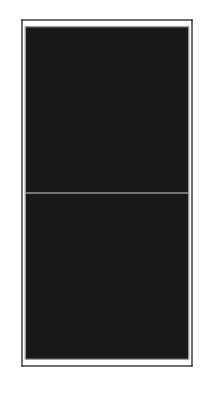
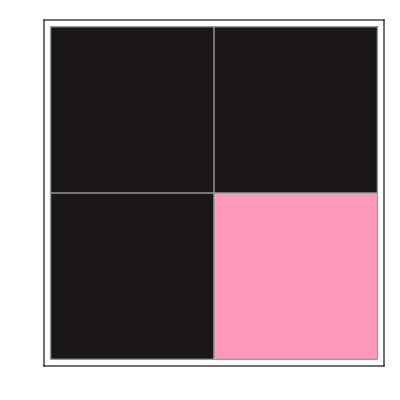
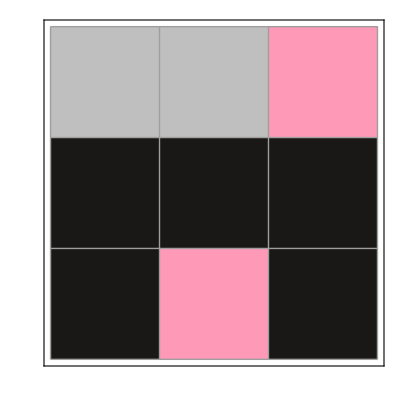
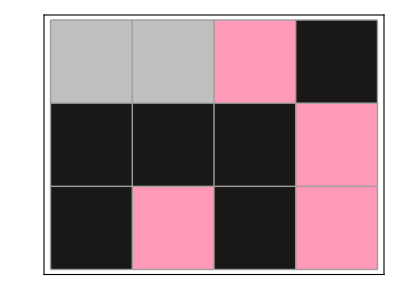
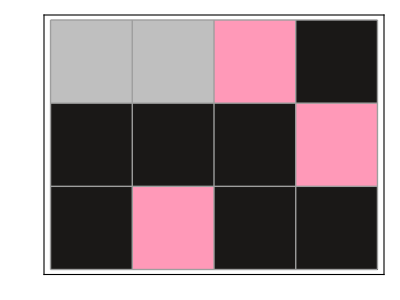
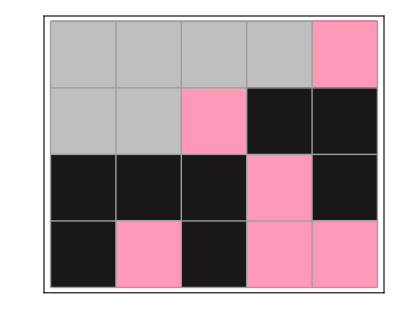
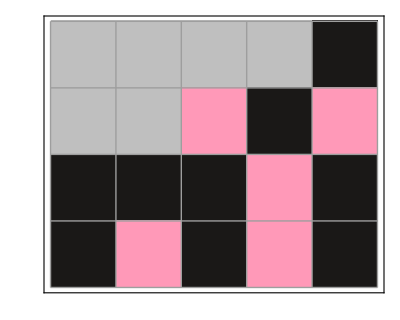
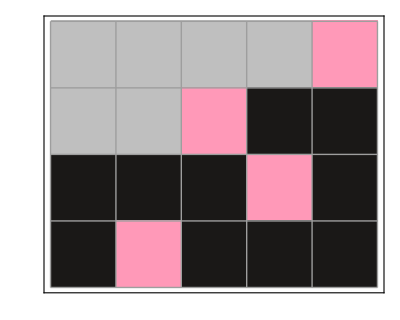
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
AllPathCanyons[NestGraph[ReplaceList[{
{left___,0,0,s___}:>{left,s,1,0,1},
{left___,1,0,s___}:>{left,s,0,1},
{left___,0,1,s___}:>{left,s,1,1,0},
{left___,1,1,s___}:>{left,s,0,1}}],{{1,1}},10,VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),GraphLayout->"LayeredDigraphEmbedding",PerformanceGoal->"Quality"]]
```

### Are certain paths within the mutliway tag system predictable? (E.g. )

### Do all paths belong to the same ‘class’ of ‘singleway’ tag system behavior (i.e. ‘explosive’, ‘degenerate’, and ‘periodic’)?